```mathematica
Clear["Global`*"]  
V[ϕ_]:=a ϕ^2-c ϕ^3+b ϕ^4;
Solve[D[V[ϕ],{ϕ,2}]==0,ϕ](*inflection point*)
```

{{ϕ→(3 c-√3 √(-8 a b+3 c^2))/(12 b)},{ϕ→(3 c+√3 √(-8 a b+3 c^2))/(12 b)}}

{0.472229,6.50146}

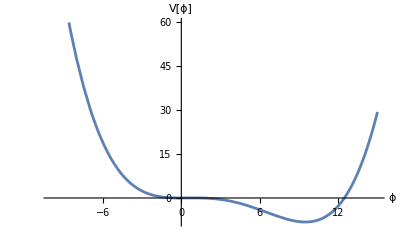

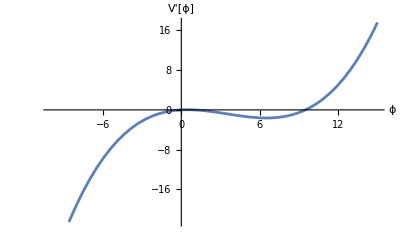

{{ϕ→0.},{ϕ→0.970553},{ϕ→9.48997}}

-8.1722

```mathematica
{a,b,c}={0.07,0.0038,0.053};
{(3 c-√3 √(-8 a b+3 c^2))/(12 b),(3 c+√3 √(-8 a b+3 c^2))/(12 b)}
Plot[V[ϕ],{ϕ,-10,15},AxesLabel->{"ϕ","V[ϕ]"}]
Plot[V'[ϕ],{ϕ,-10,15},AxesLabel->{"ϕ","V'[ϕ]"}]
phi=Solve[D[V[ϕ],{ϕ,1}]==0,ϕ]
Vmin=V[ϕ/.phi[[3]]]
```

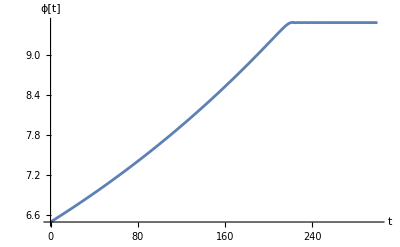

```mathematica
T=300;
m=10;
eqn=ϕ''[t]+10 √(24 Pi(1/2 m ϕ'[t]^2+V[ϕ[t]]-Vmin))ϕ'[t]+V'[ϕ[t]]==0;

sol=NDSolve[{eqn,ϕ'[0]==0,ϕ[0]==6.50146},ϕ[t],{t,0,T}];
Plot[Evaluate[ϕ[t]/.sol],{t,0,T},AxesLabel->{"t","ϕ[t]"},PlotRange->All]
```

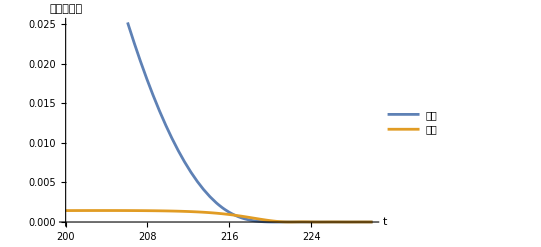

```mathematica
Po=V[ϕ[t]/. sol]-Vmin;
Ki=1/2 m (D[ϕ[t]/. sol,t])^2;
Plot[Evaluate[{Po,Ki}],{t,200,230},AxesLabel->{"t","动能，势能"},PlotLegends->Placed[{"势能","动能"}, {Top,Right}]]
```

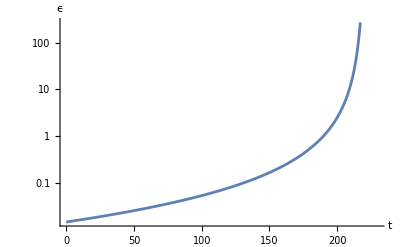

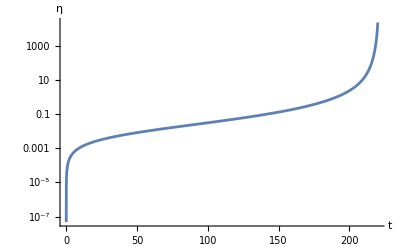

```mathematica
ϵ=1/16(V'[ϕ[t]/. sol]/(V[ϕ[t]/. sol]-Vmin))^2;
η=Abs[1/8(V''[ϕ[t]/. sol]/(V[ϕ[t]/. sol]-Vmin))];
LogPlot[Evaluate[ϵ],{t,0,230},AxesLabel->{"t","ϵ"}]
LogPlot[Evaluate[η],{t,0,220},AxesLabel->{"t","η"},PlotRange->All]
```